```mathematica
Tcn={0,0.015197864,0.017863372,0.023256351,0.024702381,0,0.028030979,0.02496124,0.018514313,0};
ntot={0.75,0.8,0.85,0.9,0.95,1.0,1.05,1.1,1.15,1.2};
```

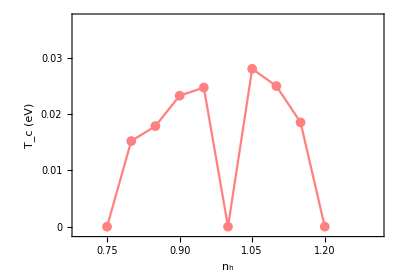

```mathematica
dcaTcvsn2by2Upp0=ListPlot[Table[{ntot[[i]],Tcn[[i]]},{i,1,Length[ntot]}],PlotMarkers->{Automatic,10},Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->17.5,FontFamily->"times New Roman"},FrameLabel->{{"T_c (eV)",None},{"n_h",None}},Joined->True,PlotRange->{{0.69,1.31},{-0.001,0.037}},FrameTicks->{{{0,0.01,0.02,0.03},Automatic},{Automatic,None}},PlotStyle->Pink]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/dcaTcvsn2by2Upp0.pdf",dcaTcvsn2by2Upp0,"PDF"];
```